# Report Projekt 1

Course code: IX1500
Date: 2025-09-15

Abdinasir Abdi, Abdabdi@kth.se
Jonas Sedig,  Jonsed@kth.se

Task 1:

## Summary

### Uppgift

I denna uppgift modelleras en partikel i xy planet som rör sig enlig följade steg: 

 U :(m,n) → (m+1,n+1) (1)
 L :(m,n) → (m+1,n−1) (2)
 
Målet med uppgiften är att räkna alla möjliga vägar från en startpunt (x, y) till en given slutpunkt (x’, y’). U omfattas som ett uppsteg medan L som ett nedsteg och varje väg är en följd av dessa två. Utöver det studeras fall med restriktioner: hur många vägar som minst rör eller korsar x-axeln, och hur många som alltid håller sig ovanför den

### Result

3.1 

A)  Varje väg från punkten (0,4) till (9,3) består av 9 steg, 4 uppsteg och 5 nedsteg. Totala antalet olika ordningar dessa steg ges av binomialkoefficienten  (9/4) = 126 vägar.

B)  Av alla möjliga vägar finns det totalt 9 vägar som berör eller passerar x-axel minste en gång.

C) Skillnaden mellan alla möjliga vägar och alla vägar som passerar rör eller korsar x-axeln, ger oss alla som aldrig berör.

126 - 9 = 117

## Formulas and Equations

### Model for cross section area

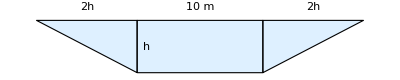

The given trapezoid area is

a(h)=(10+2h)h

x [m] | h [m] | a [m^2]
0 | 0 | 0
200 | 2.6 | 39.52
400 | 5.1 | 103.02
600 | 6.3 | 142.38
800 | 4.3 | 79.98
1000 | 2.6 | 39.52
1200 | 1.3 | 16.38
1400 | 1.7 | 22.78
1600 | 2.8 | 43.68
1800 | 1.5 | 19.5
2000 | 0 | 0

The data is interpolated as a function A(x).

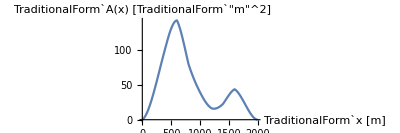

### Model for volume

The requested volume to be transported can be calculated numerically with the integral

V=∫_0^2000 A(x)dx

V≈101×10^3 m^3

I.e. about 0.1 km^3 must be transported.

## Discussion

## Code

```mathematica
ClearAll["`*"]
```

```mathematica
Binomial[9,4]//TraditionalForm
```

126

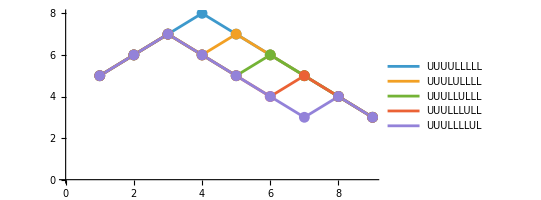

```mathematica
(*Start-och slutpunkter*)start={0,4};
goal={9,3};

(*Totalt 9 steg,4 U och 5 L*)
n=9;u=4;l=5;

(*Alla möjliga U/L-sekvenser*)
allaSteg=Subsets[Range[n],{u}];
toSeq[pos_]:=Table[If[MemberQ[pos,i],"U","L"],{i,n}];
allaVagar=toSeq/@allaSteg;

(*Funktion för att räkna koordinaterna för en sekvens*)
coords[seq_]:=Rest@FoldList[Plus,start,({1,#}&)/@(seq/. {"U"->1,"L"->-1})];

(*Välj ut några vägar och rita dem*)
ListLinePlot[coords/@Take[allaVagar,5],(*Ta 5 exempelvägar*)AxesOrigin->{0,0},AspectRatio->1/2,PlotRange->All,Mesh->All,PlotLegends->(StringJoin/@Take[allaVagar,5])]
```

Task 2: Kick Length

## Summery

### Task

A certain football path can be described by the following differential equations.

{m x''(t)=-μ x'(t) Abs[x'(t)]
m y''(t)=-m g-μ y'(t)Abs[y'(t)]

In this case, the friction force is proportional to the square of the speed v^2 and opposite to the velocity v⃗. Determine the kick angle toward the ground which gives the greatest kick length. Assume the following data:

m=0.4kg, μ=0.01 kg/m, g=9.8m/s^2

### Result

The differential equations are solved numerically for different angles and then a function L(θ) is interpolated whose maximum is determined.

L_max≈35m, θ_max≈42°

## Kick Length

### Solution to the differential equations

The angle θ is set which gives initial values (x(0),y(0))=(0,0) och (x'(0),y'(0))=v_0(cos(θ),sin(θ)). Thereafter, the differential equations are solved numerically.

{m x''(t)=-μ x'(t)√((x'(t))^2)
m y''(t)=-m g-μ y'(t)√((y'(t))^2)

The kick time t_0 is determined so that y(t_0)=0. Finally, the kick length is L=x(t_0).

The above procedure is repeated for different angles and then interpolated a function L(θ) whose maximum is determined.

L_max≈35m, θ_max≈42°

### Calculation of kick time and kick length

The time t_0 is determined so that y(t_0)=0. Finally the kick length is computed as L=x(t_0).

The solution is repeated for different angles and then interpolated a function L(θ) whose maximum is determined.

θ | 10 | 20 | 30 | 40 | 50 | 60 | 70 | 80
L | 17.2434 | 27.3526 | 32.7388 | 34.6327 | 33.6694 | 30.0809 | 23.7545 | 14.1591

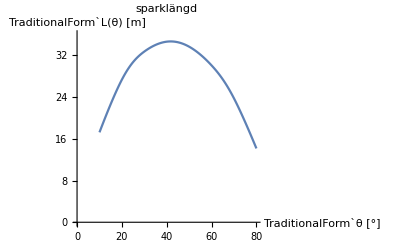

The maximum is computed as

L_max≈35m, θ_max≈41°

## Code

```mathematica
ClearAll["`*"]
```

Enter given data.

```mathematica
m=0.4;μ=0.01;g=9.8;v0=25;
```

Define differential equations and there initial conditions.

```mathematica
de[θ_]:={
m x''[t]==-μ x'[t] √(x'[t]^2),
m y''[t]==-m g-μ y'[t] √(y'[t]^2),
x[0]==0,y[0]==0,x'[0]==v0 Cos[θ],y'[0]==v0 Sin[θ]
}
```

Solve the DE.

```mathematica
sol[θ_]:=NDSolve[de[θ],{x,y},{t,0,5}]
```

Example for θ=45°

```mathematica
sol[45°]
```

```mathematica
ParametricPlot[
Evaluate[{x[t],y[t]}/.sol[45°]],{t,0,3.5},
AxesLabel->{"x","y"},PlotRange->{{0,40},{-5,15}}
]
```

The curve for different angles.

```mathematica
Manipulate[
ParametricPlot[
Evaluate[{x[t],y[t]}/.sol[θ]],{t,0,3.5},
AxesLabel->{"x","y"},
PlotLabel->StringForm["θ = `1`°",θ/Degree],
PlotRange->{{0,40},{-5,15}}
],
{{θ,45°},25°,55°}
]
```

The function for kick length.

```mathematica
len[θ_]:=Module[
{t0},
t0=t/.FindRoot[Evaluate[y[t]/.sol[θ]]==0,{t,2,4}];
First[x[t0]/.sol[θ]]
]
```

Example

```mathematica
len[45°]
```

A table for different angles.

```mathematica
data=Table[{θ,len[θ °]},{θ,10,80,10}]
```

```mathematica
TableForm[Transpose[data],TableHeadings->{{θ,L},None}]
```

```mathematica
ListLinePlot[data,InterpolationOrder->3,PlotRange->{0,36},AxesLabel->{StringForm["`1` [°]",θ],StringForm["`1` [m]",L[θ]]},PlotLabel->"sparklängd"]
```

Higher accuracy around the max value.

```mathematica
data2=Table[{θ Degree,len[θ Degree]},{θ,35,45,1}]
```

Now, search for the maximum.

```mathematica
max=FindMaximum[length[θ],{θ,40°,45°}]
```

```mathematica
θ0=(θ/.max⟦2⟧)/Degree
```